## 136 Nd

```mathematica
ClearAll["Global`*"]
```

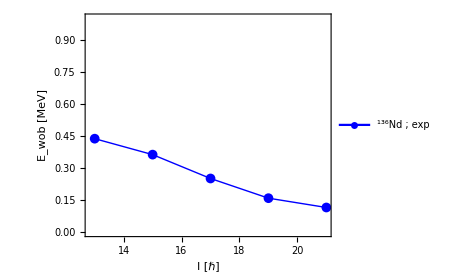

```mathematica
yrastEn=Sort[{8615,7349,6188,5189,4345,3684,3294}];
wob1En=Sort[{8098,6928,5940,5130,4452}];
yrastSpin=Table[i,{i,10,22,2}];
wob1Spin=Table[i,{i,13,21,2}];
wobbling[yrast_,b1_,spins_]:=Table[{spins[[i]],b1[[i]]/1000-1/2(yrast[[i+1]]+yrast[[i+2]])/1000},{i,1,Length[b1]}];
data=wobbling[yrastEn,wob1En,wob1Spin];
fig=ListPlot[data,Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,AspectRatio->0.8,PlotStyle->{Thick,Blue},FrameStyle->Directive[Thick,Black],FrameLabel->{"I [ℏ]","E_wob [MeV]"},LabelStyle->{18,Bold,Black},PlotLegends->Placed[{Row[{Superscript["","136"],"Nd ; exp"}]},{0.3,0.9}],ImageSize->350,PlotRange->{Full,{0,1}}];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/experimental-data-collection-wobblers/136Nd.pdf",fig];
Show[fig]
```